```mathematica
SpectralClustering1[d_, nc_:2, k_:5] := Module[{X,n, S,Si,A,L,Di,Dii,Λ,V, XX, Y, ec1, ec2, c1, c2, i, j},
    X=Round[Simplify[Standardize[d]],0.01];MatrixForm[X]; n = Length[X];
    S = Round[Simplify[Xᵀ.X / (n - 1)], 0.01]; MatrixForm[S];
   Si = Round[Simplify[Inverse[S]], 0.01];MatrixForm[Si];
   A = Table[Exp[-((X[[i]] - X[[j]]).Si.({X[[i]] - X[[j]]})ᵀ)[[1]]], {i, n}, {j, n}]; MatrixForm[A];
   Di = Table[0, {i,n}, {j,n}];Do [ Do[Di[[i]][[i]] = Di[[i]][[i]] + A[[i]][[j]], {j,n}], {i,n}];MatrixForm[Di];
   Dii = Sqrt[Inverse[Di]];L = Dii.A.Dii;MatrixForm[L];
  {Λ,V} = Eigensystem[L];MatrixForm[Λ];MatrixForm[V];
  XX = (V[[1;; k]])ᵀ;Do[XX[[i]]=Normalize[XX[[i]]],{i,n}];MatrixForm[XX];
  {ec1, ec2} = FindClusters[XX, nc, DistanceFunction-> EuclideanDistance];c1 = {}; c2 = {};   
   Do [If [MemberQ[ec1,XX[[i]]]== True, c1=Append[c1,X[[i]]],c2=Append[c2,X[[i]]]] ,{i,n}];Y = {c1, c2};
   ListLinePlot[Join[ec1,ec2]]
ListPlot3D[FindClusters[X, nc, DistanceFunction-> EuclideanDistance]]
ListPointPlot3D[FindClusters[X,nc, DistanceFunction-> EuclideanDistance]]
ListPlot3D[Y]
ListPointPlot3D[Y]
];
```

```mathematica
SpectralClustering2[d_, img_:False, k_:1,nc_:2] := Module[{X,n, w, h, S,Si,A,L1,Di,Dii,Λ,V, XX, XO,XO1,Y, ec1, ec2, c1, c2, c11, c21,i, j},
   w = h = 0;
   If [img == True, 
	w = Length[d[[1]]];h =Length[d];X = Flatten[d,1],
	X = d / Max[d](*X=Round[Simplify[Standardize[d]],0.01]*)
  ];
   MatrixForm[X];n = Length[X];
   S= Xᵀ.X / (n - 1);MatrixForm[S];
   If [Det[S]≠ 0,   Si = Round[Simplify[Inverse[S]], 0.01]; MatrixForm[Si], Si = IdentityMatrix[n]];
   A = Table[Exp[-((X[[i]] - X[[j]]).Si.({X[[i]] - X[[j]]})ᵀ)[[1]]], {i, n}, {j, n}]; MatrixForm[A];
   Di = Table[0, {i,n}, {j,n}];Do [ Do[Di[[i]][[i]] = Di[[i]][[i]] + A[[i]][[j]], {j,n}], {i,n}];MatrixForm[Di];
  (* Dii = Sqrt[Inverse[Di]];L1 = Dii.(Di-A).Dii;*)
   L1 = Inverse[Di].(Di-A);
   MatrixForm[L1];
   {Λ,V} = Eigensystem[L1];MatrixForm[Λ];MatrixForm[V];
   XX = V[[n-k]];MatrixForm[XX];
   {ec1, ec2} = FindClusters[XX, nc, DistanceFunction-> EuclideanDistance];c1 = {}; c2 = {};    
   Do [If [MemberQ[ec1,XX[[i]]]== True, c1=Append[c1,X[[i]]],c2=Append[c2,X[[i]]]] ,{i,n}]; Y = {c1, c2};XO = X;
   Do [If [MemberQ[c1,XO[[i]]]== True, XO[[i]]={0.0,0.0,0.0},] ,{i,n}];
   {c11,c21}=FindClusters[X, nc, DistanceFunction-> EuclideanDistance];XO1=X;
    Do [If [MemberQ[c11,XO1[[i]]]== True, XO1[[i]]={0.0,0.0,0.0},] ,{i,n}];
   ListLinePlot[Join[ec1,ec2]]
ListPlot3D[{c11,c21}]
ListPointPlot3D[{c11,c21}]
ListPlot3D[Y]
ListPointPlot3D[Y]
(*If [img == True, Image[Partition[XO1, w, h]],]*)
If [img == True, Image[Partition[XO, w]],]
];
```

```mathematica
DSpectralClustering2[X_,  k_:1,nc_:2] := Module[{n, w, h, S,Si,A,L1,Di,Dii,Λ,V, XX, XO,Y, ec1, ec2, c1, c2, i, j, temp},
   n = Length[X];
   S= Xᵀ.X / (n - 1);MatrixForm[S];
   If [Det[S]≠ 0,   Si = Round[Simplify[Inverse[S]], 0.01]; MatrixForm[Si], Si = IdentityMatrix[n]];
   A = Table[Exp[-((X[[i]] - X[[j]]).Si.({X[[i]] - X[[j]]})ᵀ)[[1]]], {i, n}, {j, n}]; MatrixForm[A];
   Di = Table[0, {i,n}, {j,n}];Do [ Do[Di[[i]][[i]] = Di[[i]][[i]] + A[[i]][[j]], {j,n}], {i,n}];MatrixForm[Di];
  (* Dii = Sqrt[Inverse[Di]];L1 = Dii.(Di-A).Dii;*)
   L1 = Inverse[Di].(Di-A);
   MatrixForm[L1];
   {Λ,V} = Eigensystem[L1];MatrixForm[Λ];MatrixForm[V];
   XX = V[[n-k]];MatrixForm[XX];
   {ec1, ec2} = FindClusters[XX, nc, DistanceFunction-> EuclideanDistance];
   (*If [Mean[ec1] < Mean[ec2], temp = ec1; ec1 = ec2; ec2 = temp,  ];*)
   If [Length[ec1] < Length[ec2], temp = ec1; ec1 = ec2; ec2 = temp,  ];
   c1 = {}; c2 = {};    
   Do [If [MemberQ[ec1,XX[[i]]]== True, c1=Append[c1,X[[i]]],c2=Append[c2,X[[i]]]] ,{i,n}]; Y = {c1, c2};XO = X;
   Do [If [MemberQ[c1,XO[[i]]]== True, XO[[i]]={0.0,0.0,0.0},] ,{i,n}];
   XO
];
```

```mathematica
d = {{02,14,33,50},{24,56,31,67},{23,51,31,69},{02,10,36,46},{20,52,30,65},{19,51,27,58},{13,45,28,57},{16,47,33,63},{17,45,25,49},{14,47,32,70},{02,16,31,48},{19,50,25,63},{01,14,36,49},{02,13,32,44},{12,40,26,58},{18,49,27,63},{10,33,23,50},{02,16,38,51},{02,16,30,50},{21,56,28,64},{04,19,38,51},{02,14,30,49},{10,41,27,58},{15,45,29,60},{02,14,36,50},{19,51,27,58},{04,15,34,54},{18,55,31,64},{10,33,24,49},{02,14,42,55},{15,50,22,60},{14,39,27,52},{02,14,29,44},{12,39,27,58},{23,57,32,69},{15,42,30,59},{20,49,28,56},{18,58,25,67},{13,44,23,63},{15,49,25,63},{11,30,25,51},{21,54,31,69},{25,61,36,72},{13,36,29,56},{21,55,30,68},{01,14,30,48},{03,17,38,57},{14,44,30,66},{04,15,37,51},{17,50,30,67},{22,56,28,64},{15,51,28,63},{15,45,22,62},{14,46,30,61},{11,39,25,56},{23,59,32,68},{23,54,34,62},{25,57,33,67},{02,13,35,55},{15,45,32,64},{18,51,30,59},{23,53,32,64},{15,45,30,54},{21,57,33,67},{02,13,30,44},{02,16,32,47},{18,60,32,72},{18,49,30,61},{02,12,32,50},{01,11,30,43},{14,44,31,67},{02,14,35,51},{04,16,34,50},{10,35,26,57},{23,61,30,77},{13,42,26,57},{01,15,41,52},{18,48,30,60},{13,42,27,56},{02,15,31,49},{04,17,39,54},{16,45,34,60},{10,35,20,50},{02,13,32,47},{13,54,29,62},{02,15,34,51},{10,50,22,60},{01,15,31,49},{02,15,37,54},{12,47,28,61},{13,41,28,57},{04,13,39,54},{20,51,32,65},{15,49,31,69},{13,40,25,55},{03,13,23,45},{03,15,38,51},{14,48,28,68},{02,15,35,52},{25,60,33,63},{15,46,28,65},{03,14,34,46},{18,48,32,59},{16,51,27,60},{18,55,30,65},{05,17,33,51},{22,67,38,77},{21,66,30,76},{13,52,30,67},{13,40,28,61},{11,38,24,55},{02,14,34,52},{20,64,38,79},{06,16,35,50},{20,67,28,77},{12,44,26,55},{03,14,30,48},{02,19,34,48},{14,56,26,61},{02,12,40,58},{18,48,28,62},{15,45,30,56},{02,14,32,46},{04,15,44,57},{24,56,34,63},{16,58,30,72},{21,59,30,71},{18,56,29,63},{12,42,30,57},{23,69,26,77},{13,56,29,66},{02,15,34,52},{10,37,24,55},{02,15,31,46},{19,61,28,74},{03,13,35,50},{18,63,29,73},{15,47,31,67},{13,41,30,56},{13,43,29,64},{22,58,30,65},{03,14,35,51},{14,47,29,61},{19,53,27,64},{02,16,34,48},{20,50,25,57},{13,40,23,55},{02,17,34,54},{24,51,28,58},{02,15,37,53}};
```

```mathematica
SpectralClustering2[d]
```

```mathematica
d1 = {{02,14,33,50},{24,56,31,67},{23,51,31,69},{02,10,36,46},{20,52,30,65},{19,51,27,58},{13,45,28,57},{16,47,33,63},{17,45,25,49},{14,47,32,70},{02,16,31,48},{19,50,25,63},{01,14,36,49},{02,13,32,44},{12,40,26,58},{18,49,27,63},{10,33,23,50},{02,16,38,51},{02,16,30,50},{21,56,28,64},{04,19,38,51},{02,14,30,49},{10,41,27,58},{15,45,29,60},{02,14,36,50},{19,51,27,58},{04,15,34,54},{18,55,31,64},{10,33,24,49},{02,14,42,55},{15,50,22,60},{14,39,27,52},{02,14,29,44},{12,39,27,58},{23,57,32,69},{15,42,30,59},{20,49,28,56},{18,58,25,67},{13,44,23,63},{15,49,25,63},{11,30,25,51},{21,54,31,69},{25,61,36,72},{13,36,29,56},{21,55,30,68},{01,14,30,48},{03,17,38,57},{14,44,30,66},{04,15,37,51},{17,50,30,67},{22,56,28,64},{15,51,28,63},{15,45,22,62},{14,46,30,61},{11,39,25,56},{23,59,32,68},{23,54,34,62},{25,57,33,67},{02,13,35,55},{15,45,32,64},{18,51,30,59},{23,53,32,64},{15,45,30,54},{21,57,33,67},{02,13,30,44},{02,16,32,47},{18,60,32,72},{18,49,30,61},{02,12,32,50},{01,11,30,43},{14,44,31,67},{02,14,35,51},{04,16,34,50},{10,35,26,57},{23,61,30,77},{13,42,26,57},{01,15,41,52},{18,48,30,60},{13,42,27,56},{02,15,31,49},{04,17,39,54}};
```

```mathematica
d2 = {{16,45,34,60},{10,35,20,50},{02,13,32,47},{13,54,29,62},{02,15,34,51},{10,50,22,60},{01,15,31,49},{02,15,37,54},{12,47,28,61},{13,41,28,57},{04,13,39,54},{20,51,32,65},{15,49,31,69},{13,40,25,55},{03,13,23,45},{03,15,38,51},{14,48,28,68},{02,15,35,52},{25,60,33,63},{15,46,28,65},{03,14,34,46},{18,48,32,59},{16,51,27,60},{18,55,30,65},{05,17,33,51},{22,67,38,77},{21,66,30,76},{13,52,30,67},{13,40,28,61},{11,38,24,55},{02,14,34,52},{20,64,38,79},{06,16,35,50},{20,67,28,77},{12,44,26,55},{03,14,30,48},{02,19,34,48},{14,56,26,61},{02,12,40,58},{18,48,28,62},{15,45,30,56},{02,14,32,46},{04,15,44,57},{24,56,34,63},{16,58,30,72},{21,59,30,71},{18,56,29,63},{12,42,30,57},{23,69,26,77},{13,56,29,66},{02,15,34,52},{10,37,24,55},{02,15,31,46},{19,61,28,74},{03,13,35,50},{18,63,29,73},{15,47,31,67},{13,41,30,56},{13,43,29,64},{22,58,30,65},{03,14,35,51},{14,47,29,61},{19,53,27,64},{02,16,34,48},{20,50,25,57},{13,40,23,55},{02,17,34,54},{24,51,28,58},{02,15,37,53}};
```

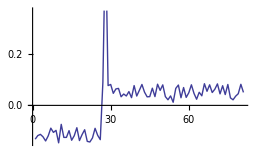
Null^2 -Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D-

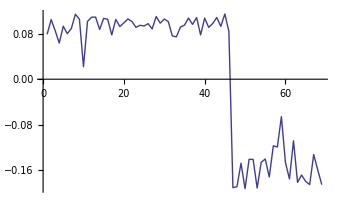
Null^2 -Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D-

```mathematica
SpectralClustering2[d1]
SpectralClustering2[d2]
```

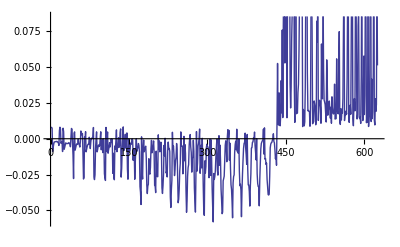
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

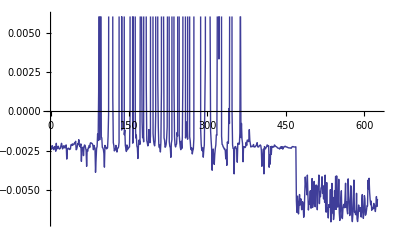
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

```mathematica
SpectralClustering2[ImageData[-Graphics-], True]
SpectralClustering2[ImageData[-Graphics-], True]
(*SpectralClustering2[ImageData[-Graphics-], True]*)
```

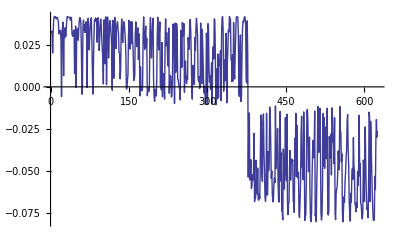
```mathematica
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-
```

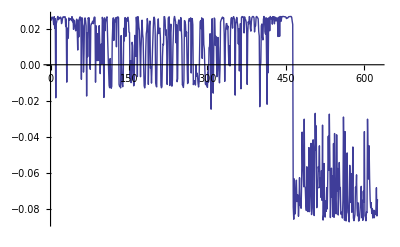
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

```mathematica
(*SpectralClustering2[ImageData[-Graphics-],True]*)(*SpectralClustering2[ImageData[-Graphics-],True]*)(*SpectralClustering2[ImageData[-Graphics-],True]*)(*SpectralClustering2[ImageData[-Graphics-],True]*)
```

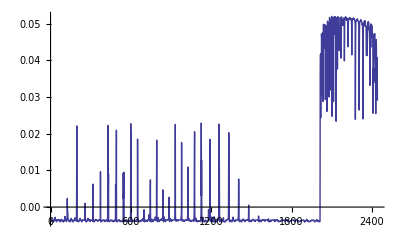
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

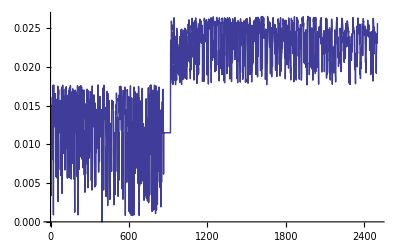
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

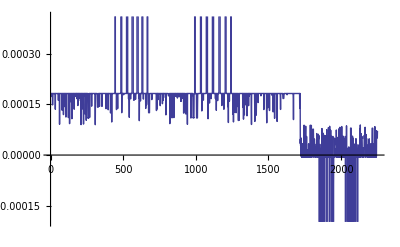
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

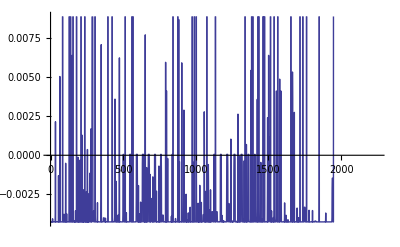
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

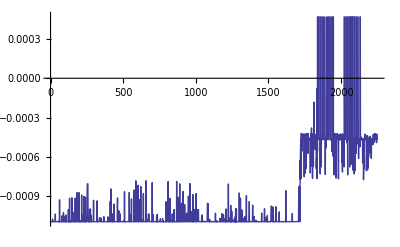
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

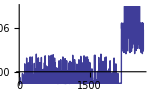
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

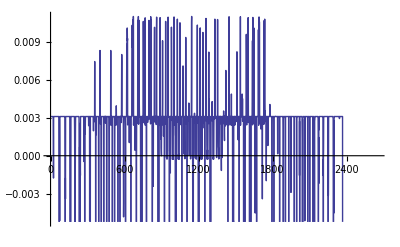
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

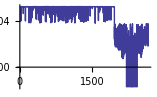
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

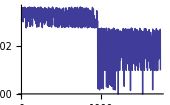
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

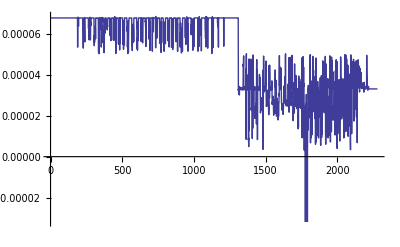
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

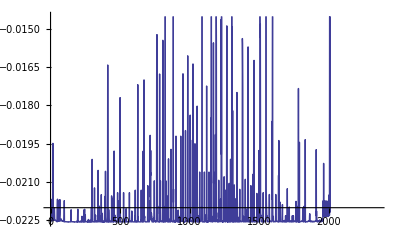
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

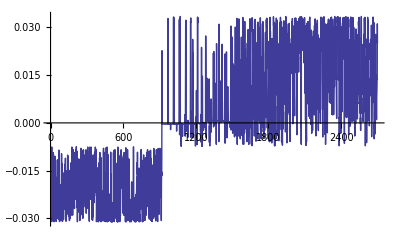
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

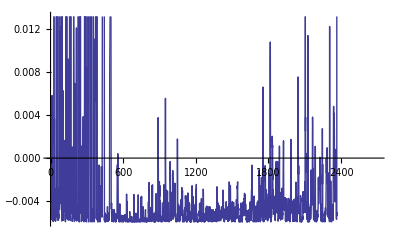
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

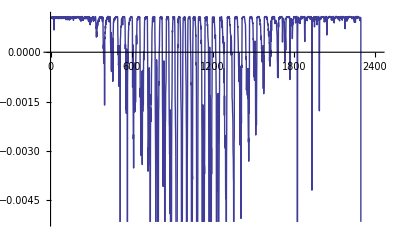
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

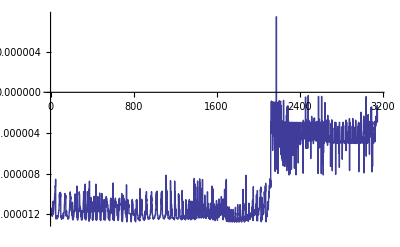
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

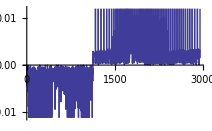
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

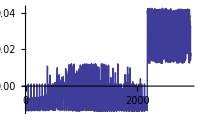
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

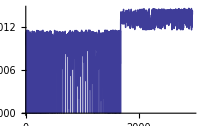
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

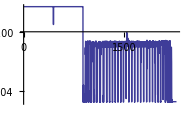
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

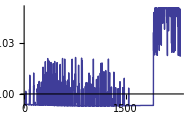
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics-

```mathematica
SpectralClustering2[ImageData[-Graphics-],True]
```

```mathematica
(*d = ImageData[-Graphics-];*)
d = ImageData[-Graphics-];
n=5;
w = Length[d[[1]]];h =Length[d];X = Flatten[d,1];Xn = Partition[X, Length[X]/n];
Do [ Xn[[i]]=DSpectralClustering2[Xn[[i]]],{i,n}];
X = Flatten[Xn,1];
Image[Partition[X, w]]
```

```mathematica
(*FormW[k_,n_,A1_]:=
Module[{i,j,sum, r0,W1,s0},
sum = 0;
W1 = Table[0,{i,n}];
For [j = k + 1, j ≤ n, ++j,
sum = sum + (A1[[j]][[ k]])^2;];
s0 = N[Sqrt[sum],6];
If [A1[[k+1]][[k]]<0, s0 = -s0;];
r0 = N[Sqrt[2.(A1[[k+1]][[k]]+s0).s0],6];
For [j = 1, j ≤ k, ++j, W1[[j]] = 0;];
W1[[k+1]] = (A1[[k+1]][[k]]+s0) / r0;
For [j = k + 2, j ≤ n, ++j, W1[[j]] = A1[[j]][[k]]/r0;]; 
{W1,s0}
];

FormV[k_,n_,A1_,W1_]:=
Module[{i,j,sum,V1},
V1 = Table[0,{i,n}];
For [j = 1, j ≤ k, ++j, V1[[j]] = 0;];
For [i = k+1, i ≤ n, ++i, 
sum = 0;
For [j = k+1, j ≤ n, ++j, 
sum = sum + A1[[i]][[j]].W1[[j]];];
V1[[i]]=sum;];
   V1
];

FormQ[k_,n_,W1_,V1_]:=
Module[{j,c,Q1},
c= 0;
Q1 = Table[0,{i,n}];
For [j = k+1, j ≤ n, ++j,
c = c + W1[[j]].V1[[j]];];
For [j = 1, j ≤ k, ++j, 
Q1[[j]] =0;];
For [j = k+1, j ≤ n, ++j, 
 Q1[[j]] =V1[[j]]-c.W1[[j]];];
Q1
];

FormA[k_,n_,Q1_,W1_,s0_]:=
Module[{i,j,A1},
A1 = Table[0,{i,n},{j,n}];
For [j = k+2, j ≤ n, ++j,
A1[[j]][[k]]=0;
A1[[k]][[j]]=0;
];
A1[[k+1]][[k]]=-s0;
A1[[k]][[k+1]]=-s0;
For [j = k, j ≤ n, ++j, 
A1[[j]][[j]] =A1[[j]][[j]]-4.Q1[[j]].W1[[j]];
];
For [i = k+1, i ≤ n, ++i, 
For [j = k+1, j ≤ n, ++j, 
 A1[[i]][[j]] =A1[[i]][[j]]-2.Q1[[j]].W1[[i]]-2.Q1[[i]].W1[[j]];
A1[[j]][[i]] =A1[[i]][[j]];
];
];
A1
];

HouseHolder[A0_]:=
Module[{i,k,n,A1,Q1,V1,W1,s0},
A1=N[A0];
n = Length[A1];
For [k=1, k ≤ n-2, ++k,
n = Length[A1];
{W1,s0}=FormW[k,n,A1];
V1=FormV[k,n,A1,W1];
Q1=FormQ[k,n,W1,V1];
A1=FormA[k,n,Q1,W1,s0];
If [k == n - 2, Print["Tri-Diagonal form: ",NumberForm[A1,10]];];
];
];

A0={{4,2,2,1},{2,-3,1,1},{2,1,3,1},{1,1,1,2}};
HouseHolder[A0]*)
```